```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
ff[n_,s_, k_] := ff[n,s,k]=N[Sum[(-1)^(j+1) j^-s ff[Floor[n/j],s,k-1],{j,2,n}]]; ff[n_, s_, 0] := UnitStep[n-1]
FAlt[n_,0,s_,a_]:=UnitStep[n-1]
FA1[n_,s_]:=FA1[n,s]=Sum[N[m^-s(-1)^(m+1)],{m,1,n}]
FAlt[n_,1,s_,a_]:=FAlt[n,1,s,a]=FA1[Floor[n],s]-FA1[a,s]
FAlt[n_,k_,s_,a_]:=FAlt[n,k,s,a]=N[Sum[Binomial[k,j] (m^-s(-1)^(m+1))^j FAlt[Floor[n/(m^j)],k-j,s, m],{j,1,k},{m,a+1,Floor[n^(1/k)]}]]
f1a[n_, s_, z_] := Sum[bin[z,k]FAlt[n,k,s,1],{k,0,Log[2,n]}]
zerosy[n_,s_]:=List@@NRoots[f1a[n,s,z]==0,z][[All,2]]
```

```mathematica
ff[1000000,N[ZetaZero[4]],4]
```

-0.998844-1.59766 ⅈ

```mathematica
N[FAlt[1000000,4,N[ZetaZero[4]],1]]
```

-0.998844-1.59766 ⅈ

```mathematica
zeros[10000000,N[ZetaZero[1]]]//TableForm
```

-2.94428+18.6403 ⅈ
0.010228-0.0117525 ⅈ
0.999973-0.0000256921 ⅈ
1.0591-4665.17 ⅈ
1.0654+6.32766 ⅈ
1.53388-5.96189 ⅈ
2.00673+0.0150723 ⅈ
2.32923-1.61325 ⅈ
2.39015-0.214322 ⅈ
2.61838+1.01077 ⅈ
3.49043-2.63485 ⅈ
3.68162+2.5122 ⅈ
6.74177-0.0210039 ⅈ
10.637-15.9654 ⅈ
11.4814+28.2677 ⅈ
16.7079-0.11017 ⅈ
20.1259+7.43797 ⅈ
26.7139-9.96327 ⅈ
47.7687+50.9779 ⅈ
55.9512-112.028 ⅈ
57.0493-34.2386 ⅈ
117.826+302.103 ⅈ
220.895-101.701 ⅈ

```mathematica
Product[ 1-1/j,{j,zeros[10000000,N[ZetaZero[1]]]}]
```

9.3841×10^-6+0.000157835 ⅈ

```mathematica
N[Pi^2/12]
```

0.822467

```mathematica
f1a[100000,-2,z]
```

0.

```mathematica
FAlt[1000,1,2,1]
```

-0.177533

```mathematica
ff[1000,2,1]
```

-0.177533

```mathematica
zeros[10000000,2]//TableForm
Product[ 1-1/j,{j,zeros[10000000,2]}]
```

-25.0413-122.576 ⅈ
-25.0413+122.576 ⅈ
-16.1421-5.78035 ⅈ
-16.1421+5.78035 ⅈ
-9.93523-14.4648 ⅈ
-9.93523+14.4648 ⅈ
-1.84852-18.1465 ⅈ
-1.84852+18.1465 ⅈ
6.14385-17.5536 ⅈ
6.14385+17.5536 ⅈ
13.4978-13.5529 ⅈ
13.4978+13.5529 ⅈ
17.6717-24.4519 ⅈ
17.6717+24.4519 ⅈ
18.979-7.16057 ⅈ
18.979+7.16057 ⅈ
20.9263
24.9227-8.541 ⅈ
24.9227+8.541 ⅈ
66.6905-49.8393 ⅈ
66.6905+49.8393 ⅈ
217.321
3721.25

0.822467+8.65515×10^-18 ⅈ

```mathematica
zeros[10000000,1]//TableForm
Product[ 1-1/j,{j,zeros[10000000,1]}]
```

-11.3964-131.995 ⅈ
-11.3964+131.995 ⅈ
-1.49532-1.34739 ⅈ
-1.49532+1.34739 ⅈ
0.112435-11.1991 ⅈ
0.112435+11.1991 ⅈ
0.378816-3.52632 ⅈ
0.378816+3.52632 ⅈ
2.78102-4.05344 ⅈ
2.78102+4.05344 ⅈ
4.6394-2.89851 ⅈ
4.6394+2.89851 ⅈ
6.2508-0.0889317 ⅈ
6.2508+0.0889317 ⅈ
17.0579
17.1421-23.8002 ⅈ
17.1421+23.8002 ⅈ
25.1407-8.23549 ⅈ
25.1407+8.23549 ⅈ
65.2672-49.4014 ⅈ
65.2672+49.4014 ⅈ
226.288
4392.01

0.693147-3.74406×10^-17 ⅈ

```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
DAlt[n_,0,s_,a_]:=UnitStep[n-1]
DA1[n_,s_]:=DA1[n,s]=Sum[N[m^-s],{m,1,n}]
DAlt[n_,1,s_,a_]:=DAlt[n,1,s,a]=DA1[Floor[n],s]-DA1[a,s]
DAlt[n_,k_,s_,a_]:=DAlt[n,k,s,a]=N[Sum[Binomial[k,j] (m^-s)^j DAlt[Floor[n/(m^j)],k-j,s, m],{j,1,k},{m,a+1,Floor[n^(1/k)]}]]
d1a[n_, s_, z_] := Sum[bin[z,k]DAlt[n,k,s,1],{k,0,Log[2,n]}]
dzeros[n_,s_]:=List@@NRoots[d1a[n,s,z]==0,z][[All,2]]
```

```mathematica
dzeros[10000000,2]//TableForm
Product[ 1-1/j,{j,dzeros[10000000,2]}]
```

$Aborted

$Aborted

```mathematica
zeros[10000000,.1I + N[ZetaZero[2]]]//TableForm
zeros[10000000,N[ZetaZero[2]]]//TableForm
zeros[10000000,-.1I + N[ZetaZero[2]]]//TableForm
```

-4204.28-2915.36 ⅈ
-11.0475+286.348 ⅈ
-5.32712+1.48361 ⅈ
-3.40911+33.033 ⅈ
-0.0107495-0.000741138 ⅈ
0.988473+0.0232957 ⅈ
1.15667-6.84743 ⅈ
2.02357+0.0186354 ⅈ
2.59232+0.150767 ⅈ
2.86791-1.04211 ⅈ
3.17251+1.58288 ⅈ
3.80794+3.28481 ⅈ
3.93298-2.70173 ⅈ
6.73833-0.031841 ⅈ
7.66962+19.7787 ⅈ
7.87704-72.2511 ⅈ
10.7394-17.0016 ⅈ
15.227-0.834028 ⅈ
15.4542+7.84042 ⅈ
25.353-20.2619 ⅈ
29.9927+52.82 ⅈ
59.6086-58.059 ⅈ
220.118-210.04 ⅈ

-4163.71-2949.26 ⅈ
-9.69325+288.018 ⅈ
-5.42227+1.48108 ⅈ
-3.22951+32.9884 ⅈ
-0.000465589+0.0106046 ⅈ
0.999991+0.0000153019 ⅈ
1.20061-6.83745 ⅈ
2.00285-0.00504836 ⅈ
2.59246+0.16043 ⅈ
2.86219-1.02459 ⅈ
3.17864+1.58091 ⅈ
3.81472+3.28919 ⅈ
3.93135-2.69123 ⅈ
6.73839-0.0316826 ⅈ
7.67628+19.7609 ⅈ
8.40552-72.5916 ⅈ
10.8025-17.0402 ⅈ
15.2951-0.811878 ⅈ
15.5569+7.8492 ⅈ
25.3491-19.8491 ⅈ
30.3968+52.894 ⅈ
59.2606-57.5567 ⅈ
219.087-207.599 ⅈ

-4122.19-2982.91 ⅈ
-8.30471+289.647 ⅈ
-5.52228+1.47999 ⅈ
-3.04785+32.9464 ⅈ
0.0105599-0.000197582 ⅈ
0.985483+0.0211906 ⅈ
1.24023-6.82881 ⅈ
1.99095-0.030665 ⅈ
2.60645+0.167777 ⅈ
2.86383-1.02044 ⅈ
3.18607+1.58045 ⅈ
3.82191+3.29378 ⅈ
3.92989-2.68576 ⅈ
6.73845-0.0315245 ⅈ
7.68215+19.7399 ⅈ
8.93876-72.9356 ⅈ
10.8527-17.0816 ⅈ
15.3584-0.79023 ⅈ
15.6566+7.85717 ⅈ
25.3637-19.4611 ⅈ
30.7939+52.9607 ⅈ
58.9415-57.0573 ⅈ
218.137-205.16 ⅈ

```mathematica
zeros[10000000,.1 + N[ZetaZero[2]]]//TableForm
zeros[10000000,N[ZetaZero[2]]]//TableForm
zeros[10000000,-.1 + N[ZetaZero[2]]]//TableForm
```

-4130.41-2908.34 ⅈ
-11.3599+289.41 ⅈ
-5.418+1.3829 ⅈ
-3.1872+33.1676 ⅈ
-0.00489119+0.0519684 ⅈ
1.05701-0.114192 ⅈ
1.19395-6.79633 ⅈ
1.90741+0.0770104 ⅈ
2.62862+0.150263 ⅈ
2.86818-1.02622 ⅈ
3.18105+1.58725 ⅈ
3.81005+3.29614 ⅈ
3.92502-2.69142 ⅈ
6.73823-0.0316248 ⅈ
7.69602+19.7687 ⅈ
8.74534-72.0589 ⅈ
10.8501-16.9829 ⅈ
15.2755-0.746169 ⅈ
15.5501+7.95078 ⅈ
24.9396-19.8295 ⅈ
30.3301+53.2981 ⅈ
58.7444-57.8882 ⅈ
216.606-208.588 ⅈ

-4163.71-2949.26 ⅈ
-9.69325+288.018 ⅈ
-5.42227+1.48108 ⅈ
-3.22951+32.9884 ⅈ
-0.000465589+0.0106046 ⅈ
0.999991+0.0000153019 ⅈ
1.20061-6.83745 ⅈ
2.00285-0.00504836 ⅈ
2.59246+0.16043 ⅈ
2.86219-1.02459 ⅈ
3.17864+1.58091 ⅈ
3.81472+3.28919 ⅈ
3.93135-2.69123 ⅈ
6.73839-0.0316826 ⅈ
7.67628+19.7609 ⅈ
8.40552-72.5916 ⅈ
10.8025-17.0402 ⅈ
15.2951-0.811878 ⅈ
15.5569+7.8492 ⅈ
25.3491-19.8491 ⅈ
30.3968+52.894 ⅈ
59.2606-57.5567 ⅈ
219.087-207.599 ⅈ

-4197.95-2990.44 ⅈ
-8.0608+286.667 ⅈ
-5.4217+1.57781 ⅈ
-3.27389+32.8065 ⅈ
-0.000116287+0.00210849 ⅈ
0.996938+0.00494952 ⅈ
1.21147-6.87775 ⅈ
1.99649-0.00103789 ⅈ
2.59247+0.1565 ⅈ
2.86586-1.02219 ⅈ
3.17634+1.57418 ⅈ
3.81896+3.28207 ⅈ
3.93754-2.68764 ⅈ
6.73855-0.0317401 ⅈ
7.65732+19.7562 ⅈ
8.06093-73.1207 ⅈ
10.7681-17.095 ⅈ
15.3194-0.877081 ⅈ
15.5668+7.74844 ⅈ
25.7402-19.8435 ⅈ
30.4704+52.497 ⅈ
59.7478-57.2222 ⅈ
221.489-206.608 ⅈ

```mathematica
zeros[10000000,.1I + N[ZetaZero[3]]]//TableForm
zeros[10000000,N[ZetaZero[3]]]//TableForm
zeros[10000000,-.1I + N[ZetaZero[3]]]//TableForm
```

-4990.67-1262.48 ⅈ
-19.4465+198.668 ⅈ
-9.84319+36.7571 ⅈ
-9.70263-59.5131 ⅈ
-3.61981+2.5083 ⅈ
0.00340154-0.00827635 ⅈ
0.822055-9.92686 ⅈ
0.982429+0.00937009 ⅈ
2.02427+0.00084531 ⅈ
2.62821+0.139758 ⅈ
2.99487-0.988604 ⅈ
3.18778+1.56269 ⅈ
3.85055+3.21737 ⅈ
4.20601-2.65992 ⅈ
6.73574-0.0382688 ⅈ
9.26501+16.1002 ⅈ
10.3973-17.0902 ⅈ
14.4101+2.61136 ⅈ
15.4866+35.1224 ⅈ
18.5597-5.43954 ⅈ
39.7484-26.2006 ⅈ
83.6147-61.5231 ⅈ
308.61-271.491 ⅈ

-4990.47-1312.75 ⅈ
-20.6692+200.738 ⅈ
-9.63863+36.6222 ⅈ
-9.30708-59.8327 ⅈ
-3.62445+2.44802 ⅈ
-0.00857301-0.00315621 ⅈ
0.764138-9.75655 ⅈ
0.999989+9.86576×10^-6 ⅈ
2.00288-0.00348785 ⅈ
2.62961+0.14334 ⅈ
2.98768-0.993729 ⅈ
3.18022+1.55855 ⅈ
3.85829+3.21508 ⅈ
4.19012-2.66475 ⅈ
6.73581-0.0381014 ⅈ
9.02819+16.0786 ⅈ
10.444-17.138 ⅈ
14.3428+2.60299 ⅈ
15.2922+35.7922 ⅈ
18.4471-5.48761 ⅈ
39.4686-26.3154 ⅈ
83.1344-61.7653 ⅈ
305.905-271.159 ⅈ

-4989.35-1362.52 ⅈ
-21.8199+202.868 ⅈ
-9.43726+36.4813 ⅈ
-8.91164-60.1528 ⅈ
-3.63147+2.3923 ⅈ
-0.00296793+0.00916663 ⅈ
0.715787-9.59469 ⅈ
0.978474+0.00660488 ⅈ
1.98284-0.0174171 ⅈ
2.6347+0.134251 ⅈ
2.97841-0.99883 ⅈ
3.18325+1.54467 ⅈ
3.87622+3.21711 ⅈ
4.17493-2.66903 ⅈ
6.73588-0.0379338 ⅈ
8.76831+16.075 ⅈ
10.4855-17.1846 ⅈ
14.2699+2.59276 ⅈ
15.1319+36.5044 ⅈ
18.3303-5.53572 ⅈ
39.1813-26.428 ⅈ
82.6431-62.0021 ⅈ
303.198-270.765 ⅈ

```mathematica
zeros[10000000,N[ZetaZero[31]]]//TableForm
zeros[10000000,N[ZetaZero[32]]]//TableForm
zeros[10000000,N[ZetaZero[33]]]//TableForm
```

-20.0507+265.966 ⅈ
-6.45622-21.9698 ⅈ
-1.05536+9.2149 ⅈ
-0.241732+3.86816 ⅈ
-0.215938-2.17054 ⅈ
0.0068937+0.0116644 ⅈ
1.00001+0.0000110904 ⅈ
1.99736-0.00218885 ⅈ
2.83533+0.393639 ⅈ
3.04595-0.670442 ⅈ
3.90502+2.11698 ⅈ
4.2368-2.87486 ⅈ
7.66246+2.1129 ⅈ
8.25611+0.503007 ⅈ
8.94342-5.68011 ⅈ
12.736-27.7639 ⅈ
25.8096-3.84079 ⅈ
34.1647+6.36382 ⅈ
61.4713+44.1556 ⅈ
79.3177-27.1908 ⅈ
157.233-132.262 ⅈ
209.517+39.6198 ⅈ
4844.16+2159.97 ⅈ

-44.6222+251.445 ⅈ
-6.64528-21.7207 ⅈ
-1.0271+9.4543 ⅈ
-0.857409-2.05595 ⅈ
-0.561243+3.97324 ⅈ
-0.00960582-0.00779953 ⅈ
1.00001+9.50978×10^-6 ⅈ
1.99818-0.00161087 ⅈ
2.92633+0.355582 ⅈ
3.17361-0.602857 ⅈ
3.85814+2.20642 ⅈ
4.41698-3.18613 ⅈ
7.1915-0.415166 ⅈ
8.60989+3.06306 ⅈ
10.3952-5.92528 ⅈ
16.5615-31.4747 ⅈ
24.1893-4.60009 ⅈ
33.1276+7.2716 ⅈ
59.1746+45.1887 ⅈ
81.4894-33.4167 ⅈ
110.989-117.393 ⅈ
212.775+27.6752 ⅈ
4889.47+1093.08 ⅈ

-60.6868+230.026 ⅈ
-6.21395-21.1772 ⅈ
-1.66418-2.33564 ⅈ
-0.986386+9.67848 ⅈ
-0.946073+4.42506 ⅈ
0.00718708+0.00208407 ⅈ
1.00001+5.84232×10^-6 ⅈ
1.99894-0.000925843 ⅈ
3.02281+0.280098 ⅈ
3.29783-0.459241 ⅈ
4.05808+2.24967 ⅈ
4.84149-3.57697 ⅈ
6.90884-0.468197 ⅈ
9.09868+3.37316 ⅈ
10.9954-5.81689 ⅈ
20.596-33.8174 ⅈ
23.6714-4.74623 ⅈ
32.2917+7.84324 ⅈ
57.1252+45.8016 ⅈ
72.3799-120.645 ⅈ
88.8028-32.8224 ⅈ
214.583+13.426 ⅈ
4803.38-79.3219 ⅈ

```mathematica
zeros[10000000,2-.1I]//TableForm
zeros[10000000,2]//TableForm
zeros[10000000,2+.1I]//TableForm
```

-26.0477+124.08 ⅈ
-24.0095-121.092 ⅈ
-16.7309-3.21318 ⅈ
-15.2691+8.25589 ⅈ
-11.5401-12.6865 ⅈ
-8.168+16.0419 ⅈ
-3.81473-17.3953 ⅈ
0.21863+18.6458 ⅈ
3.98502-17.7962 ⅈ
8.37941+17.0459 ⅈ
11.4723-14.7864 ⅈ
15.3999+12.0628 ⅈ
17.4597-9.1601 ⅈ
17.6016-24.5014 ⅈ
17.7478+24.394 ⅈ
20.1121+4.90175 ⅈ
20.7577-1.94088 ⅈ
24.9442+8.63862 ⅈ
24.9496-8.55715 ⅈ
66.662-49.9772 ⅈ
66.7206+49.7039 ⅈ
217.321+0.9084 ⅈ
3721.08+65.3744 ⅈ

-25.0413-122.576 ⅈ
-25.0413+122.576 ⅈ
-16.1421-5.78035 ⅈ
-16.1421+5.78035 ⅈ
-9.93523-14.4648 ⅈ
-9.93523+14.4648 ⅈ
-1.84852-18.1465 ⅈ
-1.84852+18.1465 ⅈ
6.14385-17.5536 ⅈ
6.14385+17.5536 ⅈ
13.4978-13.5529 ⅈ
13.4978+13.5529 ⅈ
17.6717-24.4519 ⅈ
17.6717+24.4519 ⅈ
18.979-7.16057 ⅈ
18.979+7.16057 ⅈ
20.9263
24.9227-8.541 ⅈ
24.9227+8.541 ⅈ
66.6905-49.8393 ⅈ
66.6905+49.8393 ⅈ
217.321
3721.25

-26.0477-124.08 ⅈ
-24.0095+121.092 ⅈ
-16.7309+3.21318 ⅈ
-15.2691-8.25589 ⅈ
-11.5401+12.6865 ⅈ
-8.168-16.0419 ⅈ
-3.81473+17.3953 ⅈ
0.21863-18.6458 ⅈ
3.98502+17.7962 ⅈ
8.37941-17.0459 ⅈ
11.4723+14.7864 ⅈ
15.3999-12.0628 ⅈ
17.4597+9.1601 ⅈ
17.6016+24.5014 ⅈ
17.7478-24.394 ⅈ
20.1121-4.90175 ⅈ
20.7577+1.94088 ⅈ
24.9442-8.63862 ⅈ
24.9496+8.55715 ⅈ
66.662+49.9772 ⅈ
66.7206-49.7039 ⅈ
217.321-0.9084 ⅈ
3721.08-65.3744 ⅈ

```mathematica
zeros[10000000,.5]//TableForm
```

-5.5649-136.275 ⅈ
-5.5649+136.275 ⅈ
0.0334422
0.123065-11.0902 ⅈ
0.123065+11.0902 ⅈ
0.78539
2.04628-2.66277 ⅈ
2.04628+2.66277 ⅈ
2.08928-0.787744 ⅈ
2.08928+0.787744 ⅈ
2.54582
3.35264-2.58016 ⅈ
3.35264+2.58016 ⅈ
6.74435
16.8925-23.5118 ⅈ
16.8925+23.5118 ⅈ
17.0552
25.2386-8.04952 ⅈ
25.2386+8.04952 ⅈ
64.5474-49.0656 ⅈ
64.5474+49.0656 ⅈ
230.619
4741.16

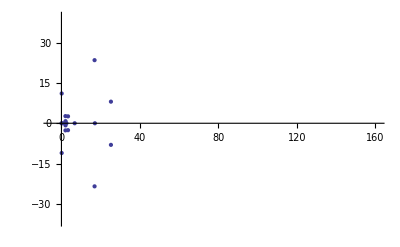

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,zeros[10000000,.5]}]]
```

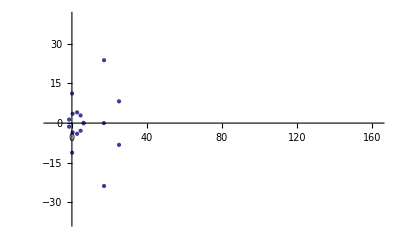

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,zeros[10000000,1]}]]
```

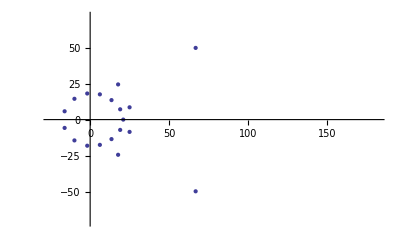

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,zeros[10000000,2]}]]
```

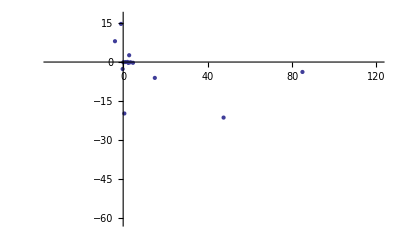

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,zeros[100000,N[ZetaZero[10]]]}]]
```

```mathematica
zeros[10000000,N[ZetaZero[100]]]//TableForm
```

-4615.92-1588.86 ⅈ
-7.84663-8.87265 ⅈ
-6.73516+12.3041 ⅈ
-3.19784+170.011 ⅈ
-2.00683-2.12074 ⅈ
0.00444354+0.000169567 ⅈ
0.999997+5.19924×10^-6 ⅈ
2.00133-0.000566946 ⅈ
2.43427-1.15814 ⅈ
2.83351-0.0603766 ⅈ
3.80246+0.433095 ⅈ
4.55094-1.4197 ⅈ
6.36689-138.999 ⅈ
7.29178+1.58652 ⅈ
8.44806+6.44521 ⅈ
9.55876-15.6586 ⅈ
9.84331-4.76613 ⅈ
17.9574+39.9512 ⅈ
19.9389+18.032 ⅈ
33.5793-10.7918 ⅈ
40.9349-31.9254 ⅈ
108.099-7.60183 ⅈ
280.984+71.0008 ⅈ

```mathematica
zeros[100000000,N[ZetaZero[100]]]//TableForm
```

-5905.92-2033.42 ⅈ
-215.271+430.476 ⅈ
-8.96512+11.7435 ⅈ
-8.25917-18.581 ⅈ
-2.92865-1.17318 ⅈ
-0.000391594+0.00173884 ⅈ
1.-3.50065×10^-7 ⅈ
1.77344-1.65967 ⅈ
1.99897-0.000385591 ⅈ
2.96919+0.141964 ⅈ
3.20758-0.593734 ⅈ
4.35534+0.425791 ⅈ
5.46722-0.37634 ⅈ
6.37063-1.97553 ⅈ
8.57171+8.48716 ⅈ
9.15015+1.90223 ⅈ
11.2755-17.7177 ⅈ
13.9419-7.18019 ⅈ
20.1989+18.1931 ⅈ
23.9654+38.2192 ⅈ
39.9825+104.366 ⅈ
45.1272-17.731 ⅈ
49.0879-32.5719 ⅈ
49.4894-141.701 ⅈ
100.886-282.796 ⅈ
131.729-6.05992 ⅈ

```mathematica
zeros[1000000000,N[ZetaZero[100]]]//TableForm
```

$Aborted

```mathematica
zerosy[1000,N[ZetaZero[1]]]//TableForm
```

-2.47962+1.04229 ⅈ
0.74741-0.0262707 ⅈ
0.890334+0.0467483 ⅈ
1.96769-0.745176 ⅈ
2.15607+0.923377 ⅈ
4.88614-0.650277 ⅈ
11.7714-1.82294 ⅈ
17.0848+15.4822 ⅈ
90.5792-53.3749 ⅈ